## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\Growth\\git\\CoChiSquare"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_]=H0 √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

## CAL

### Plot SN data with error bar

#### Import and display “SCPUnion2_AllSNe.tex”

Read the data file of SCPUnion2_mu_vs_z.txt

```mathematica
dataunionfulltmp=Import["DATA\\UNION2\\SCPUnion2_AllSNe.tex","Table"];
```

Length of dataunionfulltmp

```mathematica
lenfull=Length[dataunionfulltmp];
```

Delete the & simbols in dataunionfulltmp

```mathematica
dataunionfull=Table[{dataunionfulltmp[[i,1]],dataunionfulltmp[[i,3]],dataunionfulltmp[[i,5]],dataunionfulltmp[[i,7]],dataunionfulltmp[[i,9]],dataunionfulltmp[[i,11]],dataunionfulltmp[[i,13]],dataunionfulltmp[[i,15]]},{i,1,lenfull}];
dataunionfulltable=Grid[Join[{{Name,Redshift,Mag,Stetch,Color,Distance,Sample,CutsFails}},dataunionfull], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

#### Import and display “SCPUnion2_mu _vs _z _adjust.txt”

Import dataunion adjusted data. This data includes name, redshift, distance, error.

```mathematica
dataunion=Import["DATA\\UNION2\\SCPUnion2_mu_vs_z_adjust.txt","Table"];
datauniontable=Grid[Join[{{Name,Redshift,Distance,Error}},dataunion], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

Show dataunion table.

```mathematica
datauniontable;
```

Length of this dataunion table

```mathematica
len=Length[dataunion];
```

Simplify dataunion table and call it du

```mathematica
du=Table[{dataunion[[i,2]],dataunion[[i,3]],dataunion[[i,4]]},{i,1,len}];
dutable=Grid[Join[{{Redshift,Distance,Error}},du], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{None,None}}];
```

Show du table

```mathematica
dutable;
```

#### Visualize data.

Plot du table. That is SN

```mathematica
plunion=ErrorListPlot[du,PlotRange->All];
```

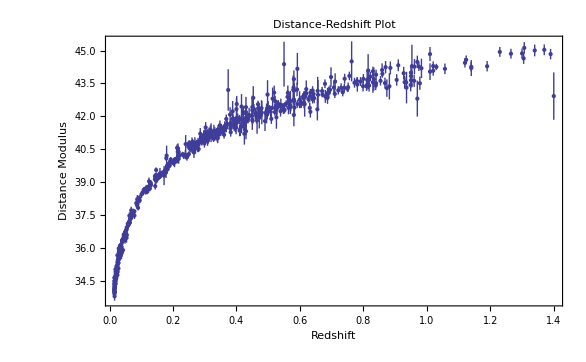

```mathematica
Show[plunion,Frame->True,FrameLabel->{"Redshift","Distance Modulus"},PlotLabel->Style["Distance-Redshift Plot",16,Orange]]
```

### Transition redshift, deceleration parameter, theoretically.

#### Theoretical Function and Values of distance/mag at different redshift.

Distance at redshift z

```mathematica
dz[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=(1+z)NIntegrate[1/hubble[Ωm0,Ωd0,Ωk0,tmp],{tmp,0,z}];
```

Magnitude calculated from distance. Theoretically of cause.

```mathematica
mag[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=5Log[10,c*dz[Ωm0,Ωd0,Ωk0,z]]+25;
```

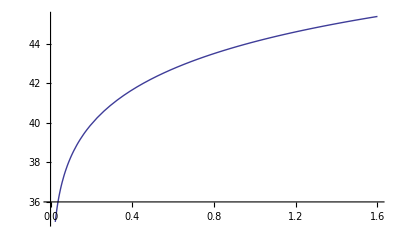

```mathematica
plmagth=Plot[mag[Ωm0w,Ωd0w,0,z],{z,0,1.6}]
```

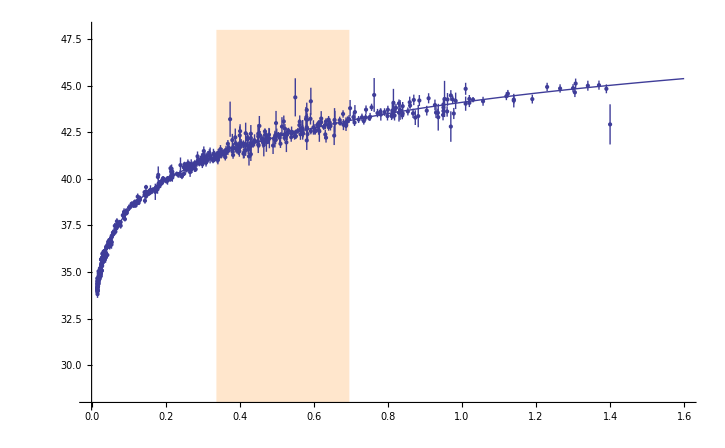

```mathematica
Show[{plunion,plmagth},PlotRange->{{0,1.6},{28,48}},AxesOrigin->{0,28},Prolog->{LightOrange,Rectangle[{0.426-0.089,28},{0.426+0.27,48}]}]
```

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,5},PlotRange->{{-1.05,5},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0}]
```

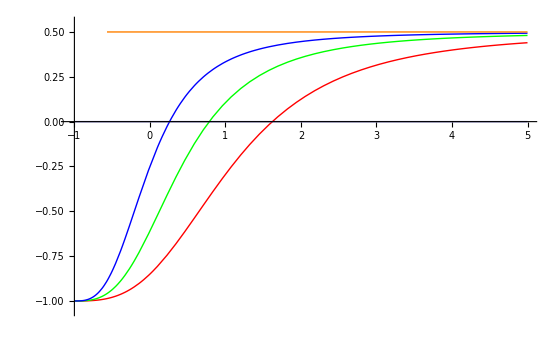

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1}]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

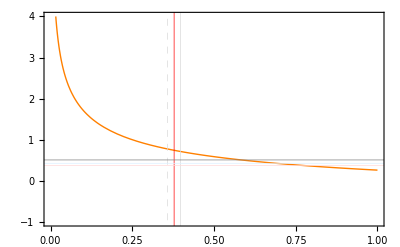

```mathematica
pldecr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

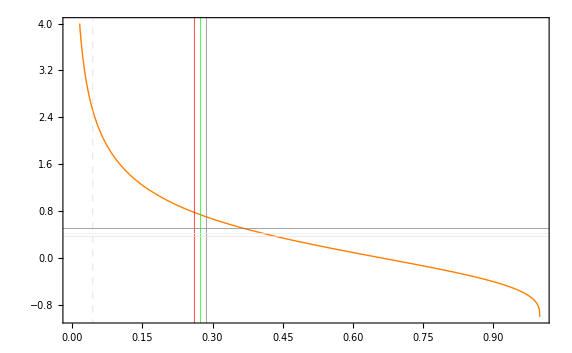

```mathematica
pldecr=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

### chi square fitting

#### Only using the error

chi square calculation.

```mathematica
chi2union[Ωm0_?NumberQ,zt_?NumberQ]:=ParallelSum[(du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]])^2/du[[i,3]]^2,{i,1,len}]
```

```mathematica
Timing[chi2union[0,0.028488]]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.093,1032.25}

#### Perform a grid method

It is unlucky that find minimum doesn’t work. SO I have to use grid method or Monte Carlo method. First try grid method.

```mathematica
chi2table=Table[{datatable[i,j]=Table[{chi2union[Ωm0,zt],Ωm0,zt},{Ωm0,i,i+0.1,0.01},{zt,j,j+0.1,0.01}],Export[StringJoin["OUTPUT\\1\\data_",ToString[i],"_",ToString[j],".dat"],datatable[i,j]]},{i,0.15,0.35,0.1},{j,0.6,0.8,0.1}];
```

```mathematica
chi2tab111=Join[chi2table[[1,1,1,1]],chi2table[[1,1,1,2]],chi2table[[1,1,1,3]],chi2table[[1,1,1,4]],chi2table[[1,1,1,5]],chi2table[[1,1,1,6]],chi2table[[1,1,1,7]],chi2table[[1,1,1,8]],chi2table[[1,1,1,9]],chi2table[[1,1,1,10]]];
chi2tab121=Join[chi2table[[1,2,1,1]],chi2table[[1,2,1,2]],chi2table[[1,2,1,3]],chi2table[[1,2,1,4]],chi2table[[1,2,1,5]],chi2table[[1,2,1,6]],chi2table[[1,2,1,7]],chi2table[[1,2,1,8]],chi2table[[1,2,1,9]],chi2table[[1,2,1,10]]];
chi2tab131=Join[chi2table[[1,3,1,1]],chi2table[[1,3,1,2]],chi2table[[1,3,1,3]],chi2table[[1,3,1,4]],chi2table[[1,3,1,5]],chi2table[[1,3,1,6]],chi2table[[1,3,1,7]],chi2table[[1,3,1,8]],chi2table[[1,3,1,9]],chi2table[[1,3,1,10]]];
chi2tab211=Join[chi2table[[2,1,1,1]],chi2table[[2,1,1,2]],chi2table[[2,1,1,3]],chi2table[[2,1,1,4]],chi2table[[2,1,1,5]],chi2table[[2,1,1,6]],chi2table[[2,1,1,7]],chi2table[[2,1,1,8]],chi2table[[2,1,1,9]],chi2table[[2,1,1,10]]];
chi2tab221=Join[chi2table[[2,2,1,1]],chi2table[[2,2,1,2]],chi2table[[2,2,1,3]],chi2table[[2,2,1,4]],chi2table[[2,2,1,5]],chi2table[[2,2,1,6]],chi2table[[2,2,1,7]],chi2table[[2,2,1,8]],chi2table[[2,2,1,9]],chi2table[[2,2,1,10]]];
chi2tab231=Join[chi2table[[2,3,1,1]],chi2table[[2,3,1,2]],chi2table[[2,3,1,3]],chi2table[[2,3,1,4]],chi2table[[2,3,1,5]],chi2table[[2,3,1,6]],chi2table[[2,3,1,7]],chi2table[[2,3,1,8]],chi2table[[2,3,1,9]],chi2table[[2,3,1,10]]];
chi2tab311=Join[chi2table[[3,1,1,1]],chi2table[[3,1,1,2]],chi2table[[3,1,1,3]],chi2table[[3,1,1,4]],chi2table[[3,1,1,5]],chi2table[[3,1,1,6]],chi2table[[3,1,1,7]],chi2table[[3,1,1,8]],chi2table[[3,1,1,9]],chi2table[[3,1,1,10]]];
chi2tab321=Join[chi2table[[3,2,1,1]],chi2table[[3,2,1,2]],chi2table[[3,2,1,3]],chi2table[[3,2,1,4]],chi2table[[3,2,1,5]],chi2table[[3,2,1,6]],chi2table[[3,2,1,7]],chi2table[[3,2,1,8]],chi2table[[3,2,1,9]],chi2table[[3,2,1,10]]];
chi2tab331=Join[chi2table[[3,3,1,1]],chi2table[[3,3,1,2]],chi2table[[3,3,1,3]],chi2table[[3,3,1,4]],chi2table[[3,3,1,5]],chi2table[[3,3,1,6]],chi2table[[3,3,1,7]],chi2table[[3,3,1,8]],chi2table[[3,3,1,9]],chi2table[[3,3,1,10]]];
```

```mathematica
chi2tabt=Join[chi2tab111,chi2tab121,chi2tab131,chi2tab211,chi2tab221,chi2tab231,chi2tab311,chi2tab321,chi2tab331];
```

Length of this joined table.

```mathematica
lenchi2tabt=Length[chi2tabt];
```

```mathematica
chi2tabtt=Table[{chi2tabt[[i,2]],chi2tabt[[i,3]],chi2tabt[[i,1]]},{i,1,lenchi2tabt}];
```

Export to save this table for future use.

```mathematica
Export["OUTPUT\\1\\chi2_table_0.15-0.45_0.6-0.9.dat",chi2tabtt]
```

OUTPUT\chi2_table_0.15-0.45_0.6-0.9.dat

A local view of the calculated chi2 data. As you see, the minimum is really hard to distingush. So I decide to write another method to do the calcualtions.

```mathematica
ListPlot3D[chi2tabtt]
```

-Graphics3D-

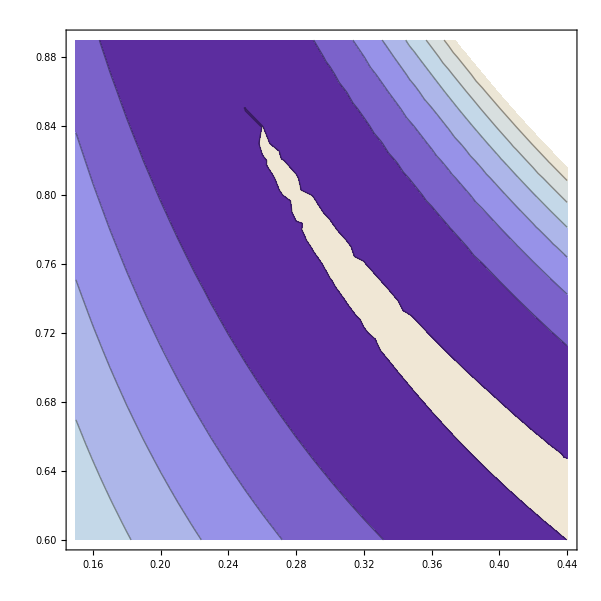

```mathematica
ListContourPlot[chi2tabtt,InterpolationOrder->1]
```